## PHAS2443: Practical Mathematics II 2017/2018 Homework 1 Hayk Khachatryan - 15013904

## Question 1a

```mathematica
Clear[eForward, eulerVs, eulerZs]

eForward[fV_,fZ_, δt_, b_, tmax_]:= 
(*
	Forward Euler intergration
	Subscript[z, n+1] = Subscript[z, n] + δt f[Subscript[t, n] , Subscript[z, n]]

inputs:
,
	fV:    dv/dt,
	fZ:    dz/dt,
	δt:   time step,
	b:    boundary conditions of form {Subscript[t, 0], Subscript[v, 0], Subscript[z, 0]},
	tmax: max value of t

output: a list of points of the form {Subscript[t, n], Subscript[v, n], Subscript[z, n]}

*)

NestList[ (* pass the forward euler scheme to nestlist as a pure function *)

{ (* #[[1]] = Subscript[t, n] ; #[[2]] = Subscript[v, n] ; #[[3]] = Subscript[z, n] *)
#[[1]] + δt,                                                                       (* Subscript[t, n+1] *)
#[[2]] + δt fV[#[[1]],#[[2]], #[[3]]],    (* Subscript[v, n+1] *)
#[[3]] + δt fZ[#[[1]], #[[2]], #[[3]]]       (* Subscript[z, n+1] *)
}&,

b,                        (* nest over boundary conditions, b, *)
Floor[tmax/δt]   (* tmax/δt times *)
] 


eulerZs[list_] := (* generates list of {Subscript[t, n], Subscript[z, n]} values from list *)
Drop[list, None, {2,2}]

eulerVs[list_] :=  (* generates list of {Subscript[t, n], Subscript[v, n]} values from list *)
Drop[list, None, {3,3}]
```

```mathematica
v̇[t_,v_, z_] :=  -1/(1+z)^2    (* dv/dt *)

ż[t_,v_,z_] :=  v    (* dz/dt *)
```

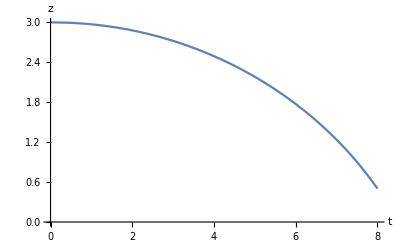

```mathematica
eulerList = (* δt = 0.1, Subscript[t, 0]= Subscript[v, 0] = 0, Subscript[z, 0]= 3 *)
eForward[v̇,ż ,0.1, {0, 0, 3}, 8];

ListPlot[
eulerZs[eulerList], 
Joined -> True,
AxesLabel->{ "t","z"}]
```

```mathematica
Clear[energyer]

energyer[list_] := 
(* 
generates list of {Subscript[t, n], Subscript[E, n]} values from list 
Subscript[E, n] = 1/2 Subscript[v, n]^2 - 1/(1+Subscript[z, n])
*)
{#[[1]], (#[[2]])^2/2 - 1/(1+ #[[3]])} & /@ list;
```

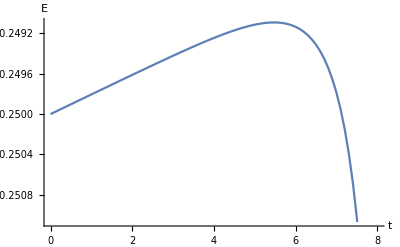

```mathematica
ListPlot[
energyer[eulerList], 
Joined-> True,
AxesLabel->{"t", "E"}]
```

## Question 1b

```mathematica
Clear[simpleVerleter, verletVs, verletZs]

simpleVerleter[fZ_,fV_, δt_, b_, tmax_]:= 
(*
	Simple Verlet intergration
,
	Subscript[z, n+1] = 2 Subscript[z, n] - Subscript[z, n-1] + δt^2 dv/dt[Subscript[t, n] , Subscript[z, n]],
	Subscript[v, n] = (Subscript[z, n+1]-Subscript[z, n-1])/(2δt)

inputs:
,
	fV:    dv/dt,
	fZ:    dz/dt,
	δt:   time step,
	b:    boundary conditions of form {Subscript[t, 0], Subscript[z, 0], Subscript[v, 0]},
	tmax: max value of t

output: a list of points of the form {Subscript[t, n], Subscript[z, n], Subscript[v, n]}

*)

list = Drop[
NestList[ (* pass the simple verlet scheme to nestlist as a pure function *)

(* { Subscript[t, n] ,  Subscript[z, n] ,   Subscript[v, n-1]  ,   Subscript[z, n-1]  , Subscript[v, n-2]} *)
(* {[[1]], [[2]], [[3]], [[4]], [5]]} *)

{ 
#[[1]] + δt,                                                                                                                        (* Subscript[t, n+1] *)
2#[[2]] -  #[[4]] + δt^2  fV[#[[1]], #[[3]], #[[2]]],                 (* Subscript[z, n+1] *)
(2#[[2]] -  #[[4]] + δt^2  fV[#[[1]], #[[3]], #[[2]]] - #[[4]])/(2δt),(* Subscript[v, n] *)
#[[2]],  (*  Subscript[z, n]*)
#[[3]]    (* Subscript[v, n-1] *)
}&,

b,                        (* nest over boundary conditions, b, *)
Floor[tmax/δt]   (* tmax/δt times *)
] ,
None,
-2];


verletZs[list_] := (* generates list of {Subscript[t, n], Subscript[z, n]} values from list *)
Drop[list, None, {3,3}]

verletVs[list_] :=  (* generates list of {Subscript[t, n], Subscript[v, n]} values from list *)
Drop[list, None, {2,2}]
```

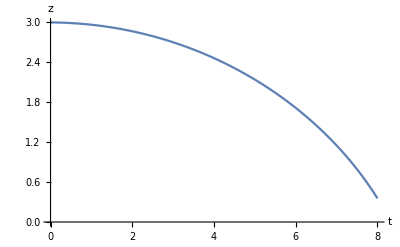

```mathematica
verletList = simpleVerleter[ż ,v̇,0.1, {0, 3, 0,3,0}, 8];
ListPlot[
verletZs[verletList], 
Joined -> True,
AxesLabel->{ "t","z"}]
```

```mathematica
Transpose[verletList][[1;;2]]
```

{{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.},{3,2.99938,2.99812,2.99625,2.99375,2.99062,2.98686,2.98248,2.97746,2.97181,2.96553,2.95861,2.95105,2.94286,2.93402,2.92453,2.91439,2.9036,2.89216,2.88006,2.86729,2.85385,2.83974,2.82495,2.80948,2.79331,2.77646,2.7589,2.74063,2.72165,2.70195,2.68152,2.66035,2.63843,2.61576,2.59232,2.56811,2.54312,2.51732,2.49072,2.4633,2.43504,2.40594,2.37597,2.34513,2.31339,2.28074,2.24717,2.21264,2.17715,2.14066,2.10317,2.06463,2.02503,1.98433,1.94252,1.89954,1.85538,1.80999,1.76334,1.71537,1.66605,1.61533,1.56314,1.50943,1.45413,1.39717,1.33847,1.27794,1.21548,1.15099,1.08433,1.01538,0.943958,0.869893,0.792969,0.712933,0.62949,0.54228,0.450866,0.354702}}

```mathematica
Append[Transpose[verletList][[1,2]],RotateLeft[Transpose[verletList][[3]]]]
```

Append::normal: Nonatomic expression expected at position 1 in Append[0.1,{-0.003125,-0.00937598,-0.0156299,-0.0218887,-0.0281543,-0.0344289,-0.0407142,-0.0470124,-0.0533255,«33»,-0.295347,-0.304044,-0.3129,-0.321922,-0.331122,-0.340509,-0.350096,-0.359894,«31»}].

Append[0.1,{-0.003125,-0.00937598,-0.0156299,-0.0218887,-0.0281543,-0.0344289,-0.0407142,-0.0470124,-0.0533255,-0.0596555,-0.0660046,-0.0723749,-0.0787685,-0.0851876,-0.0916345,-0.0981116,-0.104621,-0.111166,-0.117747,-0.124369,-0.131033,-0.137743,-0.144501,-0.15131,-0.158173,-0.165093,-0.172074,-0.179118,-0.186231,-0.193414,-0.200672,-0.20801,-0.215431,-0.22294,-0.230541,-0.23824,-0.246042,-0.253952,-0.261976,-0.270121,-0.278393,-0.286799,-0.295347,-0.304044,-0.3129,-0.321922,-0.331122,-0.340509,-0.350096,-0.359894,-0.369916,-0.380177,-0.390693,-0.401481,-0.412559,-0.423948,-0.43567,-0.44775,-0.460214,-0.473095,-0.486424,-0.500239,-0.514584,-0.529505,-0.545055,-0.561297,-0.5783,-0.596145,-0.614924,-0.634746,-0.65574,-0.678056,-0.701875,-0.727416,-0.754947,-0.7848,-0.817394,-0.853266,-0.893117,-0.93789,0}]

```mathematica
verletList
RotateLeft[#[[2]]] & /@ verletList
```

{{0,3,0},{0.1,2.99938,-0.003125},{0.2,2.99812,-0.00937598},{0.3,2.99625,-0.0156299},{0.4,2.99375,-0.0218887},{0.5,2.99062,-0.0281543},{0.6,2.98686,-0.0344289},{0.7,2.98248,-0.0407142},{0.8,2.97746,-0.0470124},{0.9,2.97181,-0.0533255},{1.,2.96553,-0.0596555},{1.1,2.95861,-0.0660046},{1.2,2.95105,-0.0723749},{1.3,2.94286,-0.0787685},{1.4,2.93402,-0.0851876},{1.5,2.92453,-0.0916345},{1.6,2.91439,-0.0981116},{1.7,2.9036,-0.104621},{1.8,2.89216,-0.111166},{1.9,2.88006,-0.117747},{2.,2.86729,-0.124369},{2.1,2.85385,-0.131033},{2.2,2.83974,-0.137743},{2.3,2.82495,-0.144501},{2.4,2.80948,-0.15131},{2.5,2.79331,-0.158173},{2.6,2.77646,-0.165093},{2.7,2.7589,-0.172074},{2.8,2.74063,-0.179118},{2.9,2.72165,-0.186231},{3.,2.70195,-0.193414},{3.1,2.68152,-0.200672},{3.2,2.66035,-0.20801},{3.3,2.63843,-0.215431},{3.4,2.61576,-0.22294},{3.5,2.59232,-0.230541},{3.6,2.56811,-0.23824},{3.7,2.54312,-0.246042},{3.8,2.51732,-0.253952},{3.9,2.49072,-0.261976},{4.,2.4633,-0.270121},{4.1,2.43504,-0.278393},{4.2,2.40594,-0.286799},{4.3,2.37597,-0.295347},{4.4,2.34513,-0.304044},{4.5,2.31339,-0.3129},{4.6,2.28074,-0.321922},{4.7,2.24717,-0.331122},{4.8,2.21264,-0.340509},{4.9,2.17715,-0.350096},{5.,2.14066,-0.359894},{5.1,2.10317,-0.369916},{5.2,2.06463,-0.380177},{5.3,2.02503,-0.390693},{5.4,1.98433,-0.401481},{5.5,1.94252,-0.412559},{5.6,1.89954,-0.423948},{5.7,1.85538,-0.43567},{5.8,1.80999,-0.44775},{5.9,1.76334,-0.460214},{6.,1.71537,-0.473095},{6.1,1.66605,-0.486424},{6.2,1.61533,-0.500239},{6.3,1.56314,-0.514584},{6.4,1.50943,-0.529505},{6.5,1.45413,-0.545055},{6.6,1.39717,-0.561297},{6.7,1.33847,-0.5783},{6.8,1.27794,-0.596145},{6.9,1.21548,-0.614924},{7.,1.15099,-0.634746},{7.1,1.08433,-0.65574},{7.2,1.01538,-0.678056},{7.3,0.943958,-0.701875},{7.4,0.869893,-0.727416},{7.5,0.792969,-0.754947},{7.6,0.712933,-0.7848},{7.7,0.62949,-0.817394},{7.8,0.54228,-0.853266},{7.9,0.450866,-0.893117},{8.,0.354702,-0.93789}}

RotateLeft::normal: Nonatomic expression expected at position 1 in RotateLeft[3].

RotateLeft::normal: Nonatomic expression expected at position 1 in RotateLeft[2.99938].

RotateLeft::normal: Nonatomic expression expected at position 1 in RotateLeft[2.99812].

General::stop: Further output of RotateLeft::normal will be suppressed during this calculation.

{RotateLeft[3],RotateLeft[2.99938],RotateLeft[2.99812],RotateLeft[2.99625],RotateLeft[2.99375],RotateLeft[2.99062],RotateLeft[2.98686],RotateLeft[2.98248],RotateLeft[2.97746],RotateLeft[2.97181],RotateLeft[2.96553],RotateLeft[2.95861],RotateLeft[2.95105],RotateLeft[2.94286],RotateLeft[2.93402],RotateLeft[2.92453],RotateLeft[2.91439],RotateLeft[2.9036],RotateLeft[2.89216],RotateLeft[2.88006],RotateLeft[2.86729],RotateLeft[2.85385],RotateLeft[2.83974],RotateLeft[2.82495],RotateLeft[2.80948],RotateLeft[2.79331],RotateLeft[2.77646],RotateLeft[2.7589],RotateLeft[2.74063],RotateLeft[2.72165],RotateLeft[2.70195],RotateLeft[2.68152],RotateLeft[2.66035],RotateLeft[2.63843],RotateLeft[2.61576],RotateLeft[2.59232],RotateLeft[2.56811],RotateLeft[2.54312],RotateLeft[2.51732],RotateLeft[2.49072],RotateLeft[2.4633],RotateLeft[2.43504],RotateLeft[2.40594],RotateLeft[2.37597],RotateLeft[2.34513],RotateLeft[2.31339],RotateLeft[2.28074],RotateLeft[2.24717],RotateLeft[2.21264],RotateLeft[2.17715],RotateLeft[2.14066],RotateLeft[2.10317],RotateLeft[2.06463],RotateLeft[2.02503],RotateLeft[1.98433],RotateLeft[1.94252],RotateLeft[1.89954],RotateLeft[1.85538],RotateLeft[1.80999],RotateLeft[1.76334],RotateLeft[1.71537],RotateLeft[1.66605],RotateLeft[1.61533],RotateLeft[1.56314],RotateLeft[1.50943],RotateLeft[1.45413],RotateLeft[1.39717],RotateLeft[1.33847],RotateLeft[1.27794],RotateLeft[1.21548],RotateLeft[1.15099],RotateLeft[1.08433],RotateLeft[1.01538],RotateLeft[0.943958],RotateLeft[0.869893],RotateLeft[0.792969],RotateLeft[0.712933],RotateLeft[0.62949],RotateLeft[0.54228],RotateLeft[0.450866],RotateLeft[0.354702]}

## Question 3

```mathematica
Clear[cycler]
cycler[list_List, nests_Integer]:=

NestList[ (* apply the algorithm to a list, keeping a history *)

ListConvolve[  (* convolute over the list with our algorithm *)

{1,1,1},  (* kernel *)
#,                   (* pure function value received from NestList *)
2,                   (* align the convolution to an element and its two neighbors *)
#,                   (* default padding value (the list) to have cyclic permutations *)
Times,          (* multiply the kernel and list elements *)

If[                   (* Returns the sum of our list element + 2 neighbors, or the Mod[sum,3] *)
(#1+#2+#3) <3,    (* if the sum of the list element and its two neighbors < 3 *)
#1+#2+#3,                 (* return the sum *)
Mod[#1+#2+#3,3]   (* else return the mod of the sum with 3 *)   
] &

] &,

list, (* passed to ListConvolve as the list *)
nests   (* how many times to nest *)
]
```

```mathematica
S = {0,0,0,0,0,1,0,0,0,0,0};
ArrayPlot[cycler[S, 150]]
```

It seems to begin repeating itself towards the end

```mathematica
Clear[distinctions]
distinctions[u_Integer]:= 
Length[                
Union[                         (* remove repeat configurations *)
cycler[S,u] (* run cycler with S and u nests *)
]]
```

```mathematica
distinctions150 = Table[distinctions[x], {x, 1, 150}];
xDistinctions150 = MapIndexed[{First[#2], #1} &, distinctions150];

ListPlot[
xDistinctions150, 
PlotLabel-> "Number of distinct automaton configurations",
AxesLabel->{"Update number", "Distinct configurations"},
Joined -> True
]

repeatBeg = (* finding where the automaton configurations start repeating *)
Position[
distinctions150,
Max[distinctions150]
][[1]][[1]];

Print["The automaton configurations begin repeating after ", repeatBeg, " updates."]
```